# HypergraphToGraph

Convert a hypergraph to a graph with the same distance matrix

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
HypergraphToGraph[list:{___List},opts:OptionsPattern[Graph]] :=Block[{i,j,l}, Graph[Flatten[Table[DirectedEdge[l[[j]],l[[i]]],{l,list},{i,Length[l]},{j,i-1}]],opts]]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

HypergraphToGraph[hg]

converts the ordered hypergraph hg to a directed graph with the same distance matrix.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

The hypergraph should be given as a list of lists, with one sublist for each hyperedge.

HypergraphToGraph takes the same options as Graph.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Convert a simple hypergraph to a graph:

```mathematica
HypergraphToGraph[{{1,3,2},{2,1,3}}]
```

-Graphics-

Find the edge list of the resulting graph:

```mathematica
EdgeList[%]
```

{1->3,1->2,3->2,2->1,2->3,1->3}

Define a more complex hypergraph:

```mathematica
hg={{1,4,2},{1,5,4},{5,2,4},{1,6,3},{2,7,6},{7,3,6},{3,8,1},{2,9,8},{9,1,8}};
```

Find the equivalent graph:

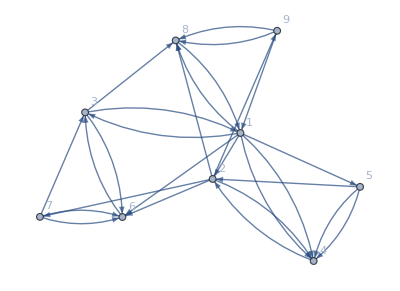

```mathematica
HypergraphToGraph[hg,VertexLabels->Automatic]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Stephen Wolfram

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

hypergraph

### Categories

Graphs & Networks

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

SymbolName (documented Wolfram Language symbol)

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

Resource Name (resources from any Wolfram repository)

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.